Alejandro Salazar Lobos		ID: 1517982
Phys362		Assignment #8

Reflection and transmission coefficients:
(For the following, n=n_t/n_i; t for transmission and i for incidence)

- Transverse electric (TE) polarization:
	Reflection coefficient: r_TE=(cos(θ_i) - √(n^2-sin^2(θ_i)))/(cos(θ_i) + √(n^2-sin^2(θ_i)))
	Transmission coefficient: t_TE=(2cos(θ_i))/(cos(θ_i) + √(n^2-sin^2(θ_i)))
- Transverse magnetic (TM) polarization:
	Reflection coefficient: r_TM=(-n^2cos(θ_i) + √(n^2-sin^2(θ_i)))/(n^2 cos(θ_i) + √(n^2-sin^2(θ_i)))
	Transmission coefficient: t_TM=(2·n·cos(θ_i))/(n^2 cos(θ_i) + √(n^2-sin^2(θ_i)))

Reflectance and transmittance:

	Reflectance: R=r^2 (r_TE or r_TM)
	
	Transmittance: T=n((cos(θ_t))/(cos(θ_i)))t^2 (t_TE or t_TM)
		
		but cos(θ_t) = √(1-sin^2(θ_t))and, by Snell’s law, n_i·sin(θ_i)=n_t·sin(θ_t)
		⟹ T=n((√(1-(n_i/n_t)^2 sin^2(θ_i)))/(cos(θ_i)))t^2=n((√(1-(1/n)^2 sin^2(θ_i)))/(cos(θ_i)))t^2=n/n((√(n^2-sin^2(θ_i)))/(cos(θ_i)))t^2
		⟹ T=((√(n^2-sin^2(θ_i)))/(cos(θ_i)))t^2

(a) Light incident from air (n_i=1.0) onto a pane of glass of index n_t=1.48. We deal with external reflection: n=n_t/n_i>1

(i) Fresnel coefficients of reflection and transmission

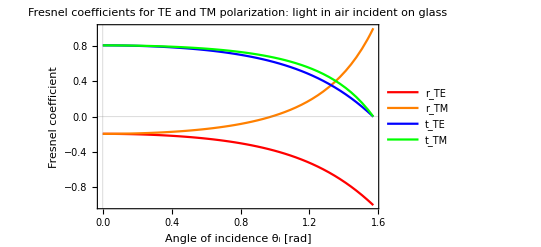

```mathematica
(* Define the equations *)

(* Indices of refraction *)
nia = 1.0; nta = 1.48;
na = nta/nia;

(* Reflection and transmission coefficients *)

(* TE polarization *)
rTEa=(Cos[theta]-Sqrt[na^2 - (Sin[theta])^2])/(Cos[theta]+Sqrt[na^2 - (Sin[theta])^2]);
tTEa=(2*Cos[theta])/(Cos[theta]+Sqrt[na^2 - (Sin[theta])^2]);
(* TM polarization *)
rTMa=(-na^2 * Cos[theta]+ Sqrt[na^2 - (Sin[theta])^2])/(na^2 * Cos[theta] + Sqrt[na^2 - (Sin[theta])^2]);
tTMa=(2*na*Cos[theta])/(na^2 * Cos[theta] + Sqrt[na^2 - (Sin[theta])^2]);

(* Graph *)
p1a1 =Plot[rTEa,{theta,0,Pi/2},PlotStyle->Red,PlotLegends->{"r_TE"},PlotRange->All,PlotTheme-> {"Scientific"},FrameLabel->{"Angle of incidence θ_i [rad]","Fresnel coefficient"},PlotLabel->"Fresnel coefficients for TE and TM polarization: light in air incident on glass"];
p2a1 = Plot[rTMa,{theta,0,Pi/2},PlotStyle->Orange,PlotLegends-> {"r_TM"},PlotRange->All];
p3a1 = Plot[tTEa,{theta,0,Pi/2},PlotStyle->Blue,PlotLegends-> {"t_TE"},PlotRange->All];
p4a1= Plot[tTMa,{theta,0,Pi/2},PlotStyle->Green,PlotLegends-> {"t_TM"},PlotRange->All];
Show[p1a1,p2a1,p3a1,p4a1,PlotRange->All]
```

Figure a-1: Fresnel coefficients of reflection and transmission for transverse electric (TE) and transverse magnetic (TM) polarization for light travelling in air (n_i=1.0) incident on glass (n_t=1.48).

```mathematica
(* Graph description *)

(* Brewster angle *)
thetaB = ArcTan[na]
```

0.976583

```mathematica
thetaB * (180/Pi)
```

55.9541

Description 1:
We have external reflection: n_i<n_t. As expected, as θ_i→ 0, r_TE=r_TM & t_TE=t_TM. For r_TE,r_TM<0, the reflected ray has a phase change of π. The brewster angle, at which all the reflected light is TE polarized, and there is no reflected TM polarized light, is θ_B=0.9765 rad ≈ 56^∘. For r_TE,r_TM>0, the reflected ray has a phase change of 0. At θ_i=90^∘, no light is transmitted into the glass, as expected, and both TE and TM polarized light have a π phase shift. There is no phase shift for transmitted light.

(ii) Reflectance and transmittance

```mathematica
(* Define the functions *)
```

```mathematica
(* TE polarization *)
RTEa=rTEa^2;
TTEa=((Sqrt[na^2 - (Sin[theta])^2])/Cos[theta])*tTEa^2;
(* TM polarization *)
RTMa=rTMa^2;
TTMa=((Sqrt[na^2 - (Sin[theta])^2])/Cos[theta])*tTMa^2;
```

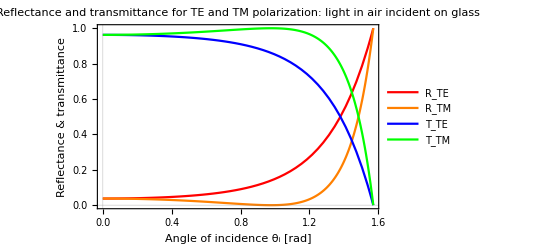

```mathematica
(* Graph *)
p1a2=Plot[RTEa,{theta,0,Pi/2},PlotStyle->Red,PlotLegends->{"R_TE"},PlotRange->All,PlotTheme->{"Scientific"},FrameLabel->{"Angle of incidence θ_i [rad]","Reflectance & transmittance"},PlotLabel->"Reflectance and transmittance for TE and TM polarization: light in air incident on glass"];
p2a2=Plot[RTMa,{theta,0,Pi/2},PlotStyle->Orange,PlotLegends->{"R_TM"},PlotRange->All];
p3a2=Plot[TTEa,{theta,0,Pi/2},PlotStyle->Blue,PlotLegends->{"T_TE"},PlotRange->All];
p4a2=Plot[TTMa,{theta,0,Pi/2},PlotStyle->Green,PlotLegends->{"T_TM"},PlotRange->All];
Show[p1a2,p2a2,p3a2,p4a2,PlotRange->All]
```

Figure a-2: Reflectance and transmittance for transverse electric (TE) and transverse magnetic (TM) polarization for light travelling in air (n_i=1.0) incident on glass (n_t=1.48).

For a comment on the following chunk of code, see “Note on TM transmittance” on page 12.

```mathematica
(* Graph description *)

(* Solve TM transmittance equation for Subscript[T, TM] = 1 *)
red1a=Reduce[TTMa==1,theta]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&(theta==-0.976583+6.28319 C[1]||theta==0.976583+6.28319 C[1])

```mathematica
(* Solve TM transmittance equation for Subscript[T, TM] > 1 *)
red2a=Reduce[TTMa==1.001,theta]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&(theta==(-0.980584+0.0536112 ⅈ)+6.28319 C[1]||theta==(0.980584-0.0536112 ⅈ)+6.28319 C[1]||theta==(-0.980584-0.0536112 ⅈ)+6.28319 C[1]||theta==(0.980584+0.0536112 ⅈ)+6.28319 C[1])

```mathematica
(* Find roots of Subscript[R, TM] *)
root1a = Reduce[RTMa==0,theta]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&(theta==-0.976583+6.28319 C[1]||theta==0.976583+6.28319 C[1])

Description 2:
(We have external reflection). As θ_i→ 0, R_TE=R_TM, since the corresponding coefficients of reflection are equal. At the brewster angle, θ_B=0.9765 rad ≈ 56^∘, the reflectance for the TM polarized light is zero: the fraction of reflected power for TM goes to zero and the reflected light is TE polarized. At θ_i=90^∘, no light is transmitted into the glass: the fraction of transmitted power goes to zero for both TE and TM polarization.

(b) Light incident from the core of an SMF-28 fiber to the cladding (core index = 1.45205; cladding index = 1.44681). We deal with internal reflection: n=n_t/n_i<1

(i) Fresnel coefficients of reflection and transmission

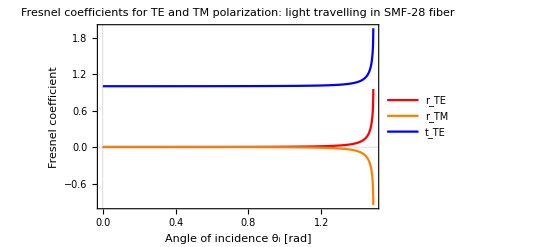

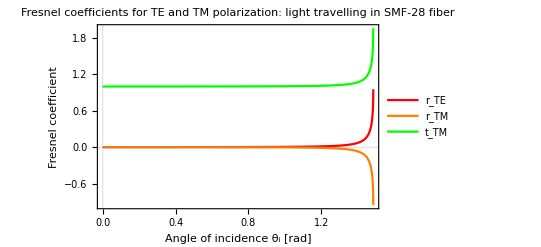

```mathematica
(* Define the indices of refraction *)
nib = 1.45205; ntb=1.44681;
nb=ntb/nib;

(* Reflection and transmission coefficients *)

(* TE polarization *)
rTEb=(Cos[theta]-Sqrt[nb^2 - (Sin[theta])^2])/(Cos[theta]+Sqrt[nb^2 - (Sin[theta])^2]);
tTEb=(2*Cos[theta])/(Cos[theta]+Sqrt[nb^2 - (Sin[theta])^2]);
(* TM polarization *)
rTMb=(-nb^2 * Cos[theta]+ Sqrt[nb^2 - (Sin[theta])^2])/(nb^2 * Cos[theta] + Sqrt[nb^2 - (Sin[theta])^2]);
tTMb=(2*nb*Cos[theta])/(nb^2 * Cos[theta] + Sqrt[nb^2 - (Sin[theta])^2]);

(* Graph *)
p1b1 =Plot[rTEb,{theta,0,Pi/2},PlotStyle->Red,PlotLegends->{"r_TE"},PlotRange->All,PlotTheme-> {"Scientific","BoldColod"},FrameLabel->{"Angle of incidence θ_i [rad]","Fresnel coefficient"},PlotLabel->"Fresnel coefficients for TE and TM polarization: light travelling in SMF-28 fiber"];
p2b1 = Plot[rTMb,{theta,0,Pi/2},PlotStyle->Orange,PlotLegends-> {"r_TM"},PlotRange->All];
p3b1 = Plot[tTEb,{theta,0,Pi/2},PlotStyle->Blue,PlotLegends-> {"t_TE"},PlotRange->All];
p4b1= Plot[tTMb,{theta,0,Pi/2},PlotStyle->Green,PlotLegends-> {"t_TM"},PlotRange->All];
(* Show[p1,p2,p3,p4,PlotRange->All] *)
Show[p1b1,p2b1,p3b1,PlotRange->All]
Show[p1b1,p2b1,p4b1,PlotRange->All]
```

Figure b-1: Fresnel coefficients of reflection and transmission for transverse electric (TE) and transverse magnetic (TM) polarization for light incident from the core of an SMF-28 fiber to the cladding (core index, n_i=1.45205; cladding index, n_t=1.44681). I decided to plot two graphs because t_TE has values that are very close to those of t_TM, so, at this scale, they look as if they overlap. A zoom in of r_TE and r_TM at the Brewster angle is provided in Figure b-2.

```mathematica
(* Graph description *)


(* Brewster angle *)
thetaB = ArcTan[nb]
```

0.783591

```mathematica
thetaB * (180/Pi)
```

44.8964

```mathematica
(* Critical angle *)
thetaC = ArcSin[nb]
```

1.48582

```mathematica
thetaC *(180/Pi)
```

85.131

Description 3:
We have internal reflection: n_i>n_t. At an angle of incidence of approximately θ_B=45^°, the Brewster angle, the reflected light is TE polarized. The critical angle of incidence, above which total internal reflection occurs, is approximately θ_C=85^°. As the incident angle goes to zero, the reflection coefficients (TE and TM) tend to be equal, and are equal at zero; the same applies to the transmission coefficients (TE and TM).

Going back to the Brewster angle. From Figure b-2 below (a zoom in of r_TE and r_TM at the Brewster angle), it can be noticed that for incident θ_i<θ_B, the reflected light undergoes no phase shift, and that at θ_B, the only light reflected is TE polarized. For θ_i>θ_B, the TM polarized light suffers a phase shift of π.

Above the critical angle: θ_i>θ_C. Figure b-1 does not go all the way to normal incidence, this is because at an incident angle larger than the critical angle, the Fresnel coefficients become complex. The same can be noticed in Figure b-3 below.

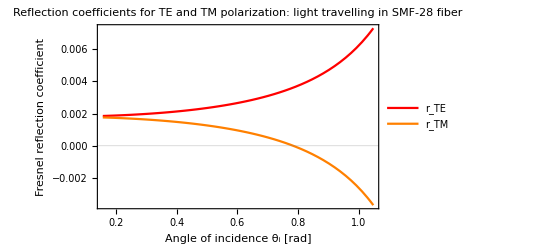

```mathematica
p1b2 =Plot[rTEb,{theta,Pi/20,Pi/3},PlotStyle->Red,PlotLegends->{"r_TE"},PlotRange->All,PlotTheme-> {"Scientific","BoldColod"},FrameLabel->{"Angle of incidence θ_i [rad]","Fresnel reflection coefficient"},PlotLabel->"Reflection coefficients for TE and TM polarization: light travelling in SMF-28 fiber"];
p2b2 = Plot[rTMb,{theta,Pi/20,Pi/3},PlotStyle->Orange,PlotLegends-> {"r_TM"},PlotRange->All];

Show[p1,p2,PlotRange->All]
```

Figure b-2: Fresnel coefficients of reflection and transmission for transverse electric (TE) and transverse magnetic (TM) polarization for light incident from the core of an SMF-28 fiber to the cladding (core index, n_i=1.45205; cladding index, n_t=1.44681). Zoom in of Figure b-1.

(ii) Reflectance and transmittance

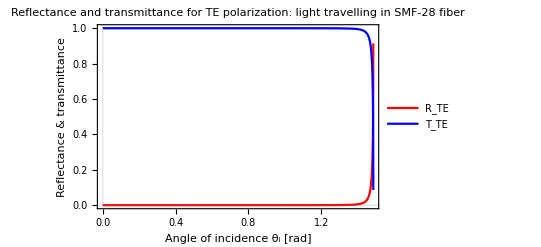

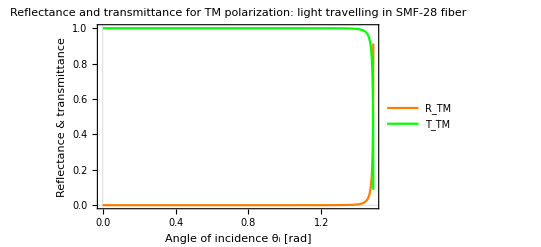

```mathematica
(* Define the functions *)

(* TE polarization *)
RTEb=rTEb^2;
TTEb=((Sqrt[nb^2 - (Sin[theta])^2])/Cos[theta])*tTEb^2;
(* TM polarization *)
RTMb=rTMb^2;
TTMb=((Sqrt[nb^2 - (Sin[theta])^2])/Cos[theta])*tTMb^2;

(* Graph *)
p1b3=Plot[RTEb,{theta,0,Pi/2},PlotStyle->Red,PlotLegends->{"R_TE"},PlotRange->All,PlotTheme->{"Scientific"},FrameLabel->{"Angle of incidence θ_i [rad]","Reflectance & transmittance"},PlotLabel->"Reflectance and transmittance for TE polarization: light travelling in SMF-28 fiber"];
p2b3=Plot[RTMb,{theta,0,Pi/2},PlotStyle->Orange,PlotLegends->{"R_TM"},PlotRange->All,PlotTheme->{"Scientific"},FrameLabel->{"Angle of incidence θ_i [rad]","Reflectance & transmittance"},PlotLabel->"Reflectance and transmittance for TM polarization: light travelling in SMF-28 fiber"];
p3b3=Plot[TTEb,{theta,0,Pi/2},PlotStyle->Blue,PlotLegends->{"T_TE"},PlotRange->All];
p4b3=Plot[TTMb,{theta,0,Pi/2},PlotStyle->Green,PlotLegends->{"T_TM"},PlotRange->All];
(* Show[p1,p2,p3,p4,PlotRange->All] *)
Show[p1b3,p3b3,PlotRange->All]
Show[p2b3,p4b3,PlotRange->All]
```

Figure b-3: Reflectance and transmittance for transverse electric (TE) and transverse magnetic (TM) polarization for light incident from the core of an SMF-28 fiber to the cladding (core index, n_i=1.45205; cladding index, n_t=1.44681).

A zoom in of Figure b-3 onto r_TE & r_TM and t_TM & t_TM:

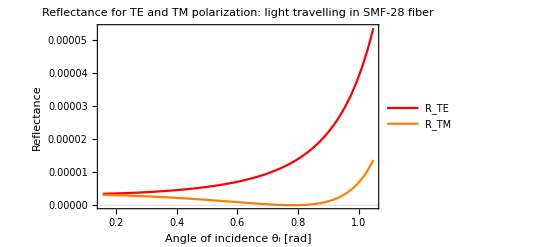

```mathematica
p1b3=Plot[RTEb,{theta,Pi/20,Pi/3},PlotStyle->Red,PlotLegends->{"R_TE"},PlotRange->All,PlotTheme->{"Scientific"},FrameLabel->{"Angle of incidence θ_i [rad]","Reflectance"},PlotLabel->"Reflectance for TE and TM polarization: light travelling in SMF-28 fiber"];
p2b3=Plot[RTMb,{theta,Pi/20,Pi/3},PlotStyle->Orange,PlotLegends->{"R_TM"},PlotRange->All,PlotTheme->{"Scientific"}];

Show[p1b3,p2b3,PlotRange->All]
```

Figure b-4: Zoom into Figure b-3 onto reflectance for TE and TM polarization.

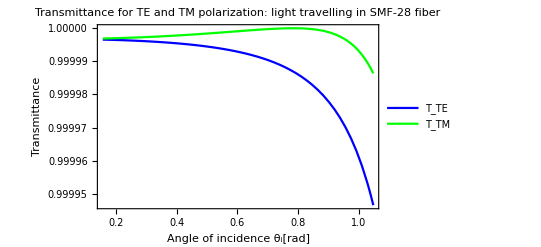

```mathematica
p3b3=Plot[TTEb,{theta,Pi/20,Pi/3},PlotStyle->Blue,PlotLegends->{"T_TE"},PlotRange->All, PlotTheme->{"Scientific"},FrameLabel->{"Angle of incidence θ_i[rad]", "Transmittance"},PlotLabel->"Transmittance for TE and TM polarization: light travelling in SMF-28 fiber"];
p4b3=Plot[TTMb,{theta,Pi/20,Pi/3},PlotStyle->Green,PlotLegends->{"T_TM"},PlotRange->All];

Show[p3b3,p4b3,PlotRange->All]
```

Figure b-5: Zoom into Figure b-3 onto transmittance for TE and TM polarization.

```mathematica
(* Graph description *)

(* Solve TM transmittance equation for Subscript[T, TM] = 1 *)
red1=Reduce[TTMb==1,theta]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&(theta==(-0.783591+1.0843×10^-6 ⅈ)+6.28319 C[1]||theta==(0.783591-1.0843×10^-6 ⅈ)+6.28319 C[1]||theta==(-0.783591-1.0843×10^-6 ⅈ)+6.28319 C[1]||theta==(0.783591+1.0843×10^-6 ⅈ)+6.28319 C[1])

```mathematica
(* Solve TM transmittance equation for Subscript[T, TM] > 1 *)
red2=Reduce[TTMb==1.000001,theta]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&(theta==(-0.817968+0.126913 ⅈ)+6.28319 C[1]||theta==(0.817968-0.126913 ⅈ)+6.28319 C[1]||theta==(-0.817968-0.126913 ⅈ)+6.28319 C[1]||theta==(0.817968+0.126913 ⅈ)+6.28319 C[1])

```mathematica
0.817968*(180/Pi)
```

46.8661

```mathematica
(* Find the roots of Subscript[R, TM] *)
root1 = Reduce[RTMb==0,theta]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&(theta==-0.78359+6.28319 C[1]||theta==0.78359+6.28319 C[1]||theta==-0.783591+6.28319 C[1]||theta==0.783591+6.28319 C[1])

Description 4:
Looking at the transmittance, from Figures b-3 to b-5, one can notice the following: below the Brewster angle, the fraction of transmitted power is almost 1 for both TE and TM polarizations, and, for the TM polarized light, it is 1 at the Brewster angle: that is no power is lost in the transmitted TM polarized wave. Looking at the reflectance: the reflected power is almost zero below the Brewster angle for both TE and TM polarized light, it is zero at θ_B for TM polarized light, and at an incident angle θ_i>θ_B, both the reflected TE and TM polarized waves drastically increase their reflectance; this makes sense, as the incident angle approaches the critical angle, we expect the reflected light to conserve the power of the original ray more and more as it approaches the point of total internal reflection. At total internal reflection, R_TE and R_TM increase their values dramatically, as can be seen in Figure b-3.

Note on TM transmittance: I am left with one question: it seems that the TM transmittance goes slightly above 1. Why is this so? Could it be due to the numerical approximations of the computer? I don’t find somewhere from where this comes from: the TM reflectance, for instance, has just one root. It seems that this happens for both TE transmittancein the light-glass and SMF-28 fiber cases.